# Feature Exploration

Moment[#1,7]&

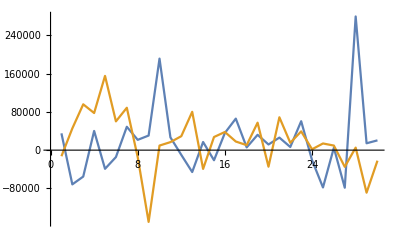

```mathematica
f=Moment[#,7]&
featYes =Table[f[reducedOxyYes80[[x,1]]],{x,30}];
featNo =Table[f[reducedOxyNo80[[x,1]]],{x,30}];
ListLinePlot[{featYes,featNo}]
```